```mathematica
Prob. de tirar 5 vegades un dau de sis cares i surti un 4 com a minim.
```

```mathematica
N[1-(5/6)^5]
```

0.598122

```mathematica
Simular 1000 tirades de 5 daus i veure quantes vegades surt com a minim un 4
```

```mathematica
simular[r_Integer,n_Integer] := Table[Random[Integer,{1,r}],{i,n}]
```

```mathematica
numeroTirades[n_Integer,o_Integer,b_Integer] := Table[simular[o,b],{i,1,n}]
```

```mathematica
numeroTirades[1000,6,5]
```

```mathematica
contarNumero[i_Integer] := N[Length[Select[numeroTirades[1000,6,5],MemberQ[#,i]&]]/1000]
```

```mathematica
contarNumero[4]
```

0.59

```mathematica
<<Combinatorica`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionaliy. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

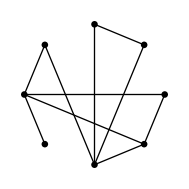

```mathematica
Ar= {{1,2},{2,3},{2,5},{2,6},{3,4},{4,5},{4,7},{4,8},{5,6},{7,8}};
```

⁃Graph:<10,8,Undirected>⁃

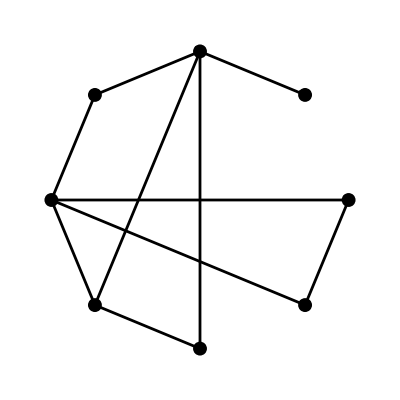

```mathematica
graf = FromUnorderedPairs[Ar]
ShowLabeledGraph[graf]
```

```mathematica
Calcul de radi, excen. i diametre
```

```mathematica
Radius[graf]
```

2

```mathematica
Eccentricity[graf]
```

{4,3,2,3,2,3,4,4}

```mathematica
Diameter[h1]
```

4